## DivideCell-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 05:31:58
using xCellerator 0.90 and XSSA 1204002

```mathematica
w=TemplateRandom[5, {{0,0}, {10,0}, {11, 10}, {-1, 10}}];
```

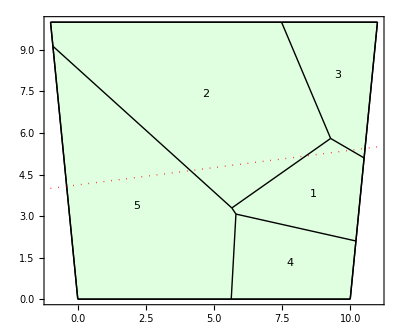

```mathematica
ShowTissue[w, "CellNumbers"-> True, Frame-> True, 
Epilog->{Thick, Red, Dotted, Line[{{-1,4}, {15, 6}}]}]
```

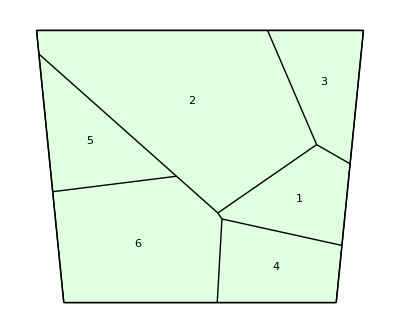

```mathematica
w1=DivideCell[w, 5, {{-1,4}, {15,6}}]; 
ShowTissue[w1, "CellNumbers"-> True]
```